```mathematica
Clear["Global`*"]
Needs["Notation`"]
Msun=2 10^33;
Mdotsol=(Msun/(3.15 10^7))
G=6.67 10^-8;
c=3 10^10;
σ=5.67 10^-5; 
kb=1.38 10^-16;
mp=1.67 10^-27;
me=9 10^-31;
κes=0.4;
Symbolize[Ṁ]
Symbolize[κ̂]
Symbolize[Subscript[M, 7]]
Symbolize[Subscript[α, 0.3]]
Symbolize[ṁ]
Symbolize[Subscript[Ṁ, Edd]]
Symbolize[Subscript[L, Edd]]
Symbolize[Subscript[R, s]]
Symbolize[Subscript[ϵ, 0.1]]

M=10^7 Msun Subscript[M, 7];
Subscript[L, Edd]=4π G M/(0.4 μe κ̂)c ;

Subscript[Ṁ, Edd]=Subscript[L, Edd]/(c^2 Subscript[ϵ, 0.1] 0.1);
Ṁ=ṁ Subscript[Ṁ, Edd];
Subscript[R, s]=2 G M/c^2;
R=10^3 Subscript[R, s] r3;

Q=G M/R^3
Teff=(3/(8π σ) (G M Ṁ)/R^3)^(1/4) //Simplify[#, Assumptions->{Subscript[M, 7]>0, r3>0}]&

Tc=8 10^4 μ0^(1/5) μe^(-1/5)r3^(-9/10) Subscript[M, 7]^(-1/5) Subscript[α, 0.3]^(-1/5) Subscript[f, T]^(1/5) ((ṁ)/Subscript[ϵ, 0.1])^(2/5) (κ̂)^(1/5) ;

Σ=(Ṁ)/(3 π (kb Tc)/(μ0 mp)0.3 Subscript[α, 0.3])(G (Subscript[M, 7] 10^7 Msun)/R^3)^(1/2) //Simplify[#, Assumptions->{Subscript[M, 7]>0, r3>0}]&
```

6.34921×10^25

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

(5.12066×10^-14)/(M_7^2 r3^3)

6229.49 ((ṁ)/(M_7 r3^3 ϵ_0.1 κ̂ μe))^(1/4)

(169.123 ((ṁ)/(ϵ_0.1))^(3/5) μ0^(4/5))/(α_0.3^(4/5) (κ̂)^(6/5) μe^(4/5) ((r3^3 f_T)/M_7)^(1/5))

```mathematica
(*Compton y parameter*)
y=4 kb Tc1/(me c^2)Max[Σ κes/2, (Σ κes/2)^2]/.{Subscript[α, 0.3]->1, μ0->0.615, μe->0.875,Subscript[ϵ, 0.1]->1, ṁ->0.1, κ̂->1, Subscript[f, T]->3/8}//Simplify
RegionPlot[y>1, {Subscript[M, 7], 0.01, 100}, {r3, 0.1 ,10}]
```

6.81481×10^-7 Tc1 Max[60.791/((r3^3/M_7)^(2/5)),7.79686/((r3^3/M_7)^(1/5))]

-Graphics-

```mathematica
Teff1=Teff/.{Subscript[α, 0.3]->1, μ0->0.615, μe->0.875,Subscript[ϵ, 0.1]->1, ṁ->0.1, κ̂->1, Subscript[f, T]->3/8};
Σ1=Σ/.{Subscript[α, 0.3]->1, μ0->0.615, μe->0.875,Subscript[ϵ, 0.1]->1, ṁ->0.1, κ̂->1, Subscript[f, T]->3/8};
Q1=Q/.{Subscript[α, 0.3]->1, μ0->0.615, μe->0.875,Subscript[ϵ, 0.1]->1, ṁ->0.1, κ̂->1, Subscript[f, T]->3/8};

Σ1/.{r3->0.1, Subscript[M, 7]->100}
Σ1/.{r3->10, Subscript[M, 7]->0.01}
Q1/.{r3->0.1, Subscript[M, 7]->0.01}
Q1/.{r3->10, Subscript[M, 7]->100}

OurDir=SetDirectory[NotebookDirectory[]]
Needs["PlotLegends`"]
ΣMax=Log[10, Σ1]/.{r3->0.1, Subscript[M, 7]->100};
ΣMin=Log[10, Σ1]/.{r3->10, Subscript[M, 7]->0.01};
QMax=Log[10, Q1]/.{r3->0.1, Subscript[M, 7]->0.01};
QMin=Log[10, Q1]/.{r3->10, Subscript[M, 7]->100};
TMin=Log[10, Teff1]/.{r3->10, Subscript[M, 7]->100};
TMax=Log[10, Teff1]/.{r3->0.1, Subscript[M, 7]->0.01};


ΣLegend= Graphics[Legend[Function[{x}, ColorData["Rainbow"][x]], 50, NumberForm[ΣMin,2]//ToString, NumberForm[ΣMax,2]//ToString, LegendShadow->False, LegendBorderSpace->2]];
QLegend= Graphics[Legend[Function[{x}, ColorData["Rainbow"][x]], 50, NumberForm[QMin,2]//ToString, NumberForm[QMax,2]//ToString, LegendShadow->False, LegendBorderSpace->2]];
TeffLegend=Graphics[Legend[Function[{x}, ColorData["Rainbow"][x]], 50, NumberForm[TMin,2]//ToString, NumberForm[TMax,2]//ToString, LegendShadow->False, LegendBorderSpace->2]];


SetOptions[ContourPlot, ImageSize->Medium];
GraphicsRow[GraphicsRow/@{{ContourPlot[Log[10,Σ1]/.{r3->10^x,Subscript[M, 7]->10^y}, {x, -1, 1}, {y,-2, 2},PlotLabel->"Suface Density Contour Plot", FrameLabel->{"Log[r_3]","Log[M_7]"} , ColorFunction->Function[{x}, ColorData["Rainbow"][x]]], ΣLegend},
{ContourPlot[Log[10, Q1]/.{r3->10^x,Subscript[M, 7]->10^y}, {x, -1, 1}, {y,-2, 2}, PlotLabel->"Q Contour Plot", FrameLabel->{"Log[r_3]","Log[M_7]"},  ColorFunction->Function[{x}, ColorData["Rainbow"][x]]], QLegend},
{ContourPlot[{ Log[10, Teff1]/.{r3->10^x,Subscript[M, 7]->10^y}}, {x, -1, 1}, {y,-2, 2}, PlotLabel->"Teff Contour Plot", FrameLabel->{"Log[r_3]","Log[M_7]"}, ColorFunction->Function[{x}, ColorData["Rainbow"][x]]], TeffLegend}}]
```

389843.

3898.43

5.12066×10^-7

5.12066×10^-21

/home/aleksey/First_Year_Project

```mathematica
0.64^(4/3)
```

0.551535

```mathematica
Tc=8 10^4 μ0^(1/5) μe^(-1/5)r3^(-9/10) M7^(-1/5) (α/0.3)^(-1/5) ft^(1/5) (mdot/(ϵ/0.1))^(2/5)  /.{μ0->0.615,μe->0.875, α->0.3, ft->3/4, ϵ->0.1, mdot->0.1}
```

28020.5/(M7^(1/5) r3^(9/10))

```mathematica
3.1 M7^(-1/5)/.{M7->10^-4}
(2.8)^(10/9)
```

19.5597

3.13937

```mathematica
ρc kb Tc/(μ0 mp)/.{μ0->0.615, Tc->10^5, ρc->1.5 10^-8}
4σ Tc^4/(3c) /.{ Tc->10^5}
cs=√(γ (4σ Tc^4/(3c ρc)))
H=Mdot/(3 π Σ cs α)/.{μ0->0.615, Tc->10^5, Σ-> 90000,Mdot->1.40 10^24, α->0.3, γ->4/3}
rul=(Solve[90000/(2 H)==ρc, ρc])[[3]]
ρc kb Tc/(μ0 mp)/.{μ0->0.615, Tc->10^5, ρc->1.5 10^-8}
4σ Tc^4/(3c) /.rul/.Tc->10^5
H/cs/.rul/.{μ0->0.615, Tc->10^5, Σ-> 90000,Mdot->1.40 10^24, α->0.3, γ->4/3}
(*H/cs/.rul


2 π/(√(G M/R^3))/.{M->Subscript[M, 7] 10^7 Msun, R->200 Subscript[R, s], Subscript[M, 7]->1}*)
```

7.78685

56474.8/(M7^(1/5) r3^(9/10))

1553.47/(M7^(4/5) r3^(18/5))

39.4141 √(γ/(M7^(4/5) r3^(18/5) ρc))

(1.20885×10^17)/(√(1/(M7^(4/5) r3^(18/5) ρc)))

{ρc→(5.1748×10^-9)/(M7^(4/15) r3^(6/5))}

56474.8/(M7^(1/5) r3^(9/10))

1553.47/(M7^(4/5) r3^(18/5))

1.3745×10^7 M7^(8/15) r3^(12/5)

2.15535×10^6

{21694.,21694.}

u^*=21694.2

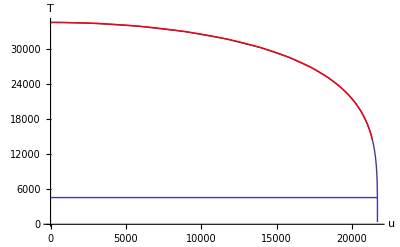

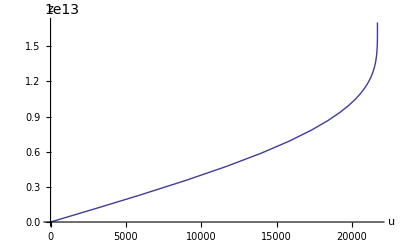

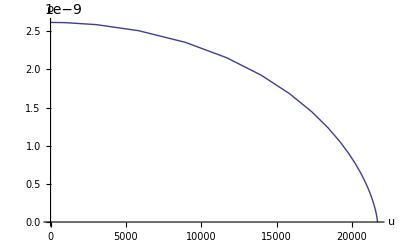

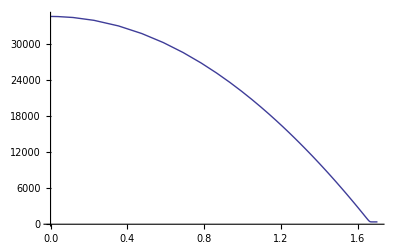

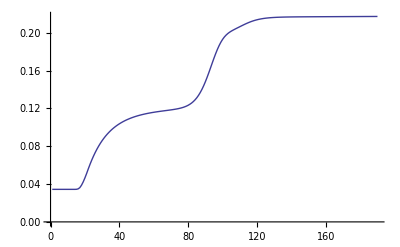

```mathematica
(*Example of a particular profile*)
M=10^7 Msun;
μe=1;
μ0=0.615;
κes=0.4 μe;
(*Import profile and extract physical parameters*)
MyFile="profile-43395-0.1-700";
MyFileP=StringSplit[MyFile, "-"]//#[[2;;]]&;
MyFileP=ToExpression/@MyFileP;
Σ=MyFileP[[1]];
Ṁ=MyFileP[[2]] 10 4 π G M/(c κes);
R=MyFileP[[3]] 2 G M/c^2;
(*Kinematic viscosity*)
ν=(Ṁ)/(3π Σ);
(*Keplerian angular velocity*)
Ω=√(G M/R^3);
(*Central sound speed*)
cs0=√(kb Tc/(μ0 mp))

Teff=((9/8 ν Σ)Ω^2/σ)^0.25;
Tss[Tc_, u_, Σ_]:=Tc(1-4(u/Σ)^2)^(1/4);
profile=Import[NotebookDirectory[]<>MyFile,"Table"];
(*Finding the points which bracket the effective temperature*)
tlow=(Position[profile[[All, 4]], x_/;x<Teff])[[1]];
thigh=(Position[profile[[All, 4]], x_/;x>Teff])[[-1]];
Extract[profile[[All,1]],{thigh, tlow}]
Print["u^*=",Σ/2 √(1-8/((3/2)κes Σ))]


u0=profile[[All,1]]//Min;
umax=profile[[All,1]]//Max;
Tc=profile[[1,4]];
t1=Show[{profile[[All,{1,4}]]}//ListLinePlot[#, PlotRange->All]&,Plot[Teff,{u,u0,umax}],PlotRange->All,AxesLabel->{"u","T"},AxesOrigin->{0,0}];
t2=Plot[Tss[Tc, u, Σ], {u,0, umax}, PlotStyle->Directive[Red]];
Show[t1, t2]
{profile[[All,{1,2}]]}//ListLinePlot[#,AxesLabel->{"u","z"}, PlotRange->All]&
{profile[[All,{1,3}]]}//ListLinePlot[#,AxesLabel->{"u","ρ"}, PlotRange->All]&
profile[[All,{2,4}]]//ListLinePlot[#,PlotRange->All,AxesOrigin->{0,0}, PlotRange->All]&
(profile[[All,6]]-profile[[All,7]])//ListLinePlot[#, AxesOrigin->{0, 0}]&
```

```mathematica
1.38 10^-23 10^9/(1.6 10^-19)
```

86250.